# Superficies de revolución

### Curvas y funciones definidas por Gray

```mathematica
cissoid[a_][t_] := 2 a {t^2, t^3}/(1 + t^2)
tractrix[a_][t_] := a {Sin[t], Cos[t] + Log[Tan[t/2]]}
catenary[a_][t_] := {a Cosh[t/a], t}
cardioid[a_][t_] := 2 a (1 + Cos[t]) {Cos[t], Sin[t]}
logspiral[a_, b_][t_] := a {Exp[b t] Cos[t], Exp[b t] Sin[t]}
cycloid[a_, b_][t_] := {a t - b Sin[t], a - b Cos[t]}

sphericalloxodrome[a_,b_][t_]:={2a Exp[b t]Cos[t],2a Exp[b t]Sin[t],-1+a^2 Exp[2b t]}/(1+a^2 Exp[2b t])

tx[A_, v_, o_ : {0, 0}] := Text[FontForm[A, {"Helvetica", 18}], v, o]

parabola[a_][t_] := {2 a t, t^2}
ellipse[a_, b_][t_] := {a Cos[t], b Sin[t]}
circ[a_] := ellipse[a, a]

Unprotect[L]; L[v_] := Sqrt[Simplify[v . v]]; Protect[L]; (*Norma*)
Unprotect[J]; J[{x_, y_}] := {-y, x}; Protect[J];(*Ortogonal*)

κ2[α_][t_] := α''[tt] . J[α'[tt]]/L[α'[tt]]^3 /. tt -> t (*Curvatura*)

arclength[α_] := Integrate[L[α'[tt]], tt] /. tt -> t
length[a_, b_][α_] := Integrate[L[α'[tt]], {tt, a, b}, GenerateConditions -> False]

lengthn[a_, b_][α_] := Module[{t}, NIntegrate[L[α'[t]], {t, a, b}]];
```

## Ahora sí

```mathematica
(*Definamos una curva en el plano yz*)
γ[t_]:={0,Cos[t],Sin[t]}
G1:=ParametricPlot3D[γ[t],{t,0,2Pi}]
(*Para rotar, definamos la matriz*)
R[θ_]:=RotationMatrix[θ,{0,0,1}]
X[u_,v_]:=R[v].γ[u]
StringForm["La parametrización es X(u,v)=``",X[u,v]]
G2=ParametricPlot3D[X[u,v],{u,0,2Pi},{v,0,2Pi},Boxed->False,Axes->False,PlotRange->All]
```

La parametrización es X(u,v)={-Cos[u] Sin[v],Cos[u] Cos[v],Sin[u]}

-Graphics3D-

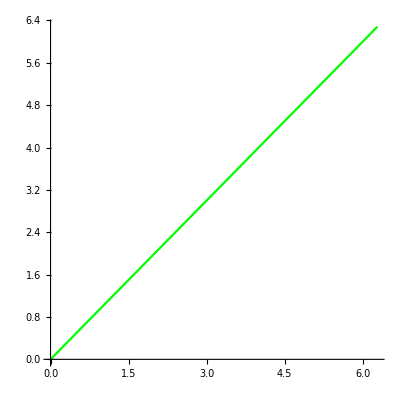
{-Graphics-,-Graphics3D-}

```mathematica
(*Definamos una curva β en el dominio de la parametrización*)
β[t_]:={t,t}
(*Y la levantamos a la superficie componiendo con la parametrización*)
α[t_]:=X[β[t][[1]],β[t][[2]]]

G3:=ParametricPlot[β[t],{t,0,2Pi},PlotStyle->{Green}](*Gráfica de la curva en R2*)
G4:=ParametricPlot3D[α[t],{t,0,2Pi},PlotStyle->{Green}] (*Gráfica de la curva en la superficie*)

{G3,Show[G2,G4,Boxed->False,Axes->False,PlotRange->All,ImageSize->Medium]}
```

```mathematica
(*El siguiente paso es calcular la primera forma fundamental*)
Xu:=D[X[u,v],u]
Xv:=D[X[u,v],v]
A:=Xu.Xu
F:=Xu.Xv
G:=Xv.Xv

(*Formateamos el output para poder leerlo*)
Print[Column[{,StringForm["``=``",Subscript[X,u],Xu],StringForm["``=``",Subscript[X,v],Xv],StringForm["E=<``,``>=``",Subscript[X,u],Subscript[X,u],A],StringForm["F=<``,``>=``",Subscript[X,u],Subscript[X,v],F],StringForm["G=<``,``>=``",Subscript[X,v],Subscript[X,v],G]}]]

(*Aquí simplemente definimos las funciones que evaluan la primera forma fundamental sobre la curva β*)
A1:=A/.{u->β[t][[1]],v->β[t][[2]]}
F1:=F/.{u->β[t][[1]],v->β[t][[2]]}
G1:=G/.{u->β[t][[1]],v->β[t][[2]]}

(*La longitud de la curva α ya en la superficie*)
Long[β_]:=Integrate[Sqrt[A1*β'[t][[1]]+2*F1*β'[t][[1]]β'[t][[2]]+G1*β'[t][[2]]],{t,0,2Pi}]
StringForm["Long(α)= ``",Long[β]]
```

X_u={Sin[u] Sin[v],-Cos[v] Sin[u],Cos[u]}
X_v={-Cos[u] Cos[v],-Cos[u] Sin[v],0}
E=<X_u,X_u>=Cos[u]^2+Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2
F=<X_u,X_v>=0
G=<X_v,X_v>=Cos[u]^2 Cos[v]^2+Cos[u]^2 Sin[v]^2

Long(α)= 4 √2 EllipticE[1/2]